Keyhole modeling for the temperature field. This is some of the first trials for the simple source terms that include different point and line moving sources. The basics are explained inside the book “Keyhole Welding: The Solid and Liquid Phases” by Alexander Kaplan.

## Steady State 3d Solutions based on Moving Point Sources of Heat:

```mathematica
A = 0.4;  (*absorptance*)
PL = 150;  (*power*)
K = 20;   (* conductivity *)
κ =  10; (* thermal diffusivity *)
Ta = 298; (* ambient temperature *)
T[x_,y_,z_]:= Ta + 2 A PL/K Sqrt[x^2+y^2+z^2]Exp[-v[x+Sqrt[x^2+y^2+z^2]]/(2 κ)]
```

Rosenthal solution for the line source model

The solution for the temperature field T(r,ϕ) in the polar coordinates is given by the analytical solution:
T(r,ϕ) = T_a+P'/2 πλ_th K_o(Pe *r) exp(-Pe * r *cos(ϕ)) where Pe is modified Peclet number:
Pe = ⋁/2κ, T_a - ambient temperature, λ_th is the thermal diffusivity, K_0() is the modified Bessel function
of second kind and zeroth order. The temperature has a singularity at the origin, where the line source
with power per unit depth P is located.
The previous equation can be calculated to explicitly give the strength P’ which is necessary to reach evaporation of the arbitrary point in polar coordinates. 
P’(r,ϕ) = (T_v-T_a) 2 πλ_th 1/(K_o(Pe * r))exp(Pe * r cos(ϕ))

The heat flow is determined by Fourier’s law of heat conduction that can be simplified by considering only of the radial component:
q = -λ_th ∇T = -λ_th(∂T)/(∂r)
Spatial derivation of the temperature of the Rosenthal solution with respect to r leads to:
∂T/∂r = P' (r, ϕ)/(2 πλ_th)Pe'[-K_0(Pe' r) cos(ϕ) + (K')_0(Pe*r)]exp(-Pe r cos(ϕ))
K'_o(x) = -K_1(x)
q(r,ϕ) = -λ_th∂T/∂r = P’(r,ϕ)/2π Pe'(K_0(Pe'r) cos(ϕ) + K_1(Pe'r)) exp(-Pe'r cos(ϕ))

If we consider the boundary condition that the evaporation temperature Tv shall be reached at 
keyhole wall.
q_v(r,ϕ) = (T_v-T_a)λ_th Pe'(cos(ϕ)+K_1(Pe'r)/K_0(Pe'r))
Keyhole profile in the x-z plane only the azimuthal angle ϕ=0,π are of interest, describing the heat
loses of any point xf at the front wall (ϕ=0)
q_v(x_r)=(T_v-T_a)λ_th Pe'(-1 + K_1(Pe’ x_r)/K_0(Pe’ x_r))

```mathematica
Pe = v/(2κ);
qvf[xf_]:= (Tv-Ta)λ Pe (-1+BesselK[1,Pe * xf])/BesselK[0,Pe xf];
qvr[xr_] := (Tv-Ta)λ Pe (1+BesselK[1, Pe * xr]) /BesselK[0, Pe xr];
```

The intensity of the laser beam with only Fresnel absorption:

```mathematica
I0=2 PL/(rf0^2 π);
Intensity[x_,z_]:= I0 * (rf/rf0)^2 Exp[-2 r^2/rf^2];
rf0 = 2 F*M^2/π;
```

Beam radius is varying over the depth by:

```mathematica
zr = 2 rf0 *F;
rf[z_]:= rf0(1+((z-z0)/zr)^2)^(1/2)
```

-Graphics--Graphics-

According the figure local energy balance at the keyhole wall is given by:
tan(θ_w) = q_v/I_a=f(x,z)
which we will give angle θ_w. I_ais the intensity at the wall.

For further absorption we will have additional plasma absorption due to Bremsstralung and
Fresnel absorption during multiple reflections Iamr:

```mathematica
tanθw =( qv[x,z]-IaiB[x,z]-Iamr[x,z] )/IaFr[θw];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

## Algorithm for the calculation

For every z_i at keyhole wall calculate downwards for both walls:
	Calculate new x (r) coordinate from the previous step.
	For every slice calculate the location of the moving line source (which is different than beam axis)
	   Distance x_fand x_r decide about the  position of the line source x_0to satisfy the general equation for the qv flow.
	   Calculate the new θ_w from  the absorbed power to the laser intensity Ia.
	   The algorithm is finished when back and front wall start cross. 

This calculation should be done two times. The first time only with I_a  we get the first description of the keyhole. The second run then estimate different absorption mechanisms and yields the final keyhole profile.

```mathematica
Clear[x];
```

```mathematica
rf0 = 2*1064 10^-6 F M^2/π
```

0.0203209

```mathematica
(* laser power *)
I0=2 PL/(rf0^2 π);
rf0 =2 wave F M^2/π;
(* absorption by the vapour plume / damping by plasma plume *)
Subscript[α, pl] = 1-Exp[-Subscript[α, iB] * Subscript[h, pl]];
(* the first run plasma absorption by Bremsstralung *)
Subscript[α, iB1] = 1-Exp[-Subscript[α, iB]d/2];
(*partial absorption of the intensity*)
Subscript[α, iBmr]=1-Exp[-Subscript[α, iB] 3d/2];


Clear[Iamrl, IaiBl];
calculateBremsMRefl[x_List,z_, θ_List]:= Module[{αpl=Subscript[α, pl], αiB1=Subscript[α, iB1],αFr = Subscript[α, Fr],αiBmr=Subscript[α, iBmr]},
zr = 2 rf0 *F;
rf[z]:= rf0(1+((z-z0)/zr)^2)^(1/2);

Ia[x,z]:= I0 * (rf[z]/rf0)^2 Exp[-2 x^2/rf[z]^2];
Iamrl[𝓍_,z,α_]:= (1-αpl)(1-αiB1)*(1-αFr)α *Ia[𝓍,z];
IaiBl[𝓍_,z,α_]:= (1-αpl)(αiB1+αiBmr *(1-αiB1)(1-αFr)(1-α) )*Ia[𝓍,z];
(* calculation of the reflection with average angle θ *)
Subscript[ρ, mr]= Subscript[ρ, Fr]^(π/(4θ)-1);
Subscript[α, mr] = 1-Subscript[ρ, mr];
MapThread[(Iamrl[#1,z,#2] + IaiBl[#1,z,#2])&,{x,Subscript[α, mr]}]
];
```

Calculate the absorption of the laser:

```mathematica
calculateAbsorption[x_List,z_, θ_List,power_]:= Module[{I0 = 2 power/(rf0^2 π),αpl=Subscript[α, pl] ,αiB1=Subscript[α, iB1]},
zr = 2 rf0 *F;
rf[z]:= rf0(1+((z-z0)/zr)^2)^(1/2);
Ia[𝓍_,z]:= I0 * (rf[z]/rf0)^2 Exp[-2 𝓍^2/rf[z]^2];
(*Ia[x,z]:= I0 * Exp[-2 x^2/rf[z]^2];*)
IaFr[𝓍_,z, α_]:= (1-αpl)(1-αiB1)*αFr[π/2-α]*Ia[𝓍,z];
MapThread[IaFr[#1,z,#2]&,{x,θ}]
];
```

Find the power for particular position of the keyhole wall, it returns two results.

```mathematica
Clear[findPower];
findPower[v_, κ_, xk_List,Ta_,Tv_,𝒜_,d_,λ_]:= Module[{xr=xk[[1]],xf=xk[[2]],x0},
Pl[r_,θ_]:=(Tv-Ta)2π λ  d/𝒜 1/BesselK[0, v r/(2κ)] Exp[v r Cos[θ]/(2κ)];
fr=FindRoot[Pl[Abs[xr-x0],π]==Pl[xf-x0,0],{x0,xr,xf}];
{Re[Pl[xf-x0/.fr,0]], Re[x0/.fr]}]
```

Calculate modified Peclet number for the problem:

```mathematica
Pe = v/(2κ);
```

Calculate the front and back heat fluxes based on the Rosental’s solution:

```mathematica
qvf[xf_]:= (Tv-Ta)λ Pe (1+BesselK[1,Pe * xf])/BesselK[0,Pe xf];
qvr[xr_] := (Tv-Ta)λ Pe (-1+BesselK[1, Pe * xr]) /BesselK[0, Pe xr];
```

Do simplified version of the above functions:

```mathematica
qvcr[rkh_]:= (Tv-Ta)λ κ/2 (v * rkh/(2 κ))^-0.7;
qvcf[rkh_]:= (Tv-Ta) λ κ/2  (2+(v * rkh/(2 κ))^-0.7);
```

Tricky part find the rear and front position of the keyhole in x, z plane by finding were the temperature reaches evaporation temperature.Note this is the moving line source and d-parameter is representing depth/thickness of the plate.

```mathematica
findRearAndFront[v_, κ_, Ta_,Tv_, 𝒜_, power_,xk_List, off_,d_,λ_]:= Module[{xrstart=-2, xfstart=(xk[[1]]+xk[[2]]) / 2
, xfmin=xk[[1]], xfmax =xk[[2]],r,θ},
Tn[x_,y_]:=Ta + (𝒜 power)/(2π λ d)Exp[-v x/(2 κ)] BesselK[0,v* Norm[{x,y}]/(2 κ)];
(* find point where temperature is Tv *)
xr=NSolve[Tn[x,0]==Tv, x,Reals];
{x/.xr[[1]],x/.xr[[2]]}
];
```

Test some of the previous functions :

```mathematica
x1={-0.5511059201951887,-0.004411116479318331};p1=2660.3611639948417;off1=-0.11137274624218212;
```

```mathematica
xl =findRearAndFront[v,κ, Ta,Tv,αFr[π/2-0.1],4000,{-3,1},off1, d, λ]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{-0.0423758,0.0311167}

```mathematica
calculateAbsorption[{-0.0015122920605260045,0.0014746971476816383},0.02, {π/2,π/3}, 4000]
```

{6027.63,6078.23}

```mathematica
calculateBremsMRefl[x1,2, {0.3,0.4}]
```

{0.980199 Ia[-0.551106,2] (0.240428+0.426701 (1-0.5 ((59.2 Cos[θ])/(459.29+29.6 Cos[θ]+Cos[θ]^2)+(59.2 Cos[θ])/(1+29.6 Cos[θ]+459.29 Cos[θ]^2)))^1.61799 (1-α_Fr))+0.744532 (1-(1-0.5 ((59.2 Cos[θ])/(459.29+29.6 Cos[θ]+Cos[θ]^2)+(59.2 Cos[θ])/(1+29.6 Cos[θ]+459.29 Cos[θ]^2)))^1.61799) Ia[-0.551106,2] (1-α_Fr),0.980199 Ia[-0.00441112,2] (0.240428+0.426701 (1-0.5 ((59.2 Cos[θ])/(459.29+29.6 Cos[θ]+Cos[θ]^2)+(59.2 Cos[θ])/(1+29.6 Cos[θ]+459.29 Cos[θ]^2)))^0.963495 (1-α_Fr))+0.744532 (1-(1-0.5 ((59.2 Cos[θ])/(459.29+29.6 Cos[θ]+Cos[θ]^2)+(59.2 Cos[θ])/(1+29.6 Cos[θ]+459.29 Cos[θ]^2)))^0.963495) Ia[-0.00441112,2] (1-α_Fr)}

```mathematica
findPower[v,κ,xl, Ta,Tv,αFr[π/2-0.1],d, λ]
```

{4000.,-1.15221×10^-17}

```mathematica
qv = {qvr[Abs[#1]], qvf[#2]}& @@ xl
```

{956.198,1306.86}

```mathematica
Ia[#,0]& /@ xl
```

{Ia[-0.153749,0],Ia[-0.0802561,0]}

```mathematica
IaFr[Abs[#],0]& /@ xl
```

{{0.140051 Ia[0.153749,0],0.0868871 Ia[0.153749,0]},{0.140051 Ia[0.0802561,0],0.0868871 Ia[0.0802561,0]}}

Here is the main algorithm to calculate the shape of the keyhole :

```mathematica
δz = 0.005; 𝒳={}; 𝒵={}; 𝒪={}; 𝒫={}; ℛ=ℛ𝒸={}; Θ = {};
(* initialize parameters *)
power=PL; offset = 0; eps=10^-3; xkh={-1,0.5}; θ={0.01,0.01};
xkh = findRearAndFront[v,κ,Ta,Tv, αFr[π/2-0.1],power, xkh, offset, d, λ];
Print["Walls:", xkh];
rkh = xkh[[2]]-xkh[[1]];
For[step=0, step < 1, step=step+1,
Print["Step: ",step];
For[z=0, z <d, z = z+δz,
(* xkh = findRearAndFront[v,κ,Ta,Tv, Subscript[α, Fr],power, xkh, offset, d, λ]; *)
(* xkh = findRearAndFront[v,κ,Ta,Tv, αFr[π/2-0.1],power, xkh, offset, d, λ]; *)
If[Max[Abs[xkh]]> 10, Break[]];
(* calculate the shape of keyhole, the heat losses *)
(* qv = {qvcr[Abs[rkh]], qvcf[rkh]}; *)
qv = {Re[qvr[Abs[#1]]], Re[qvf[#2]]}& @@ xkh;

(* tanθw =( qv-IaiB[x,z]-Iamr[x,z] )/IaFr[x,z]; *)
Print["Values:" ,qv];
Ifrens=calculateAbsorption[Abs[xkh],z, θ,power];
(* Print[Ifrens,z,xkh]; *)
If[step == 1,
(*Ic = calculateBremsMRefl[xkh,z,θ]; Print[Ic, θ]*),
Ic = {0.0,0.0}];
tanθw = qv/Ifrens;
xkh = xkh - δz*Re[tanθw];(*  Print["New:",xkh,{offset,power}]; *)
rkh = xkh[[2]]-xkh[[1]]; xc = rkh/2.0;

avθ = Mean[θ];
{power, offset} =findPower[v,κ, xkh, Ta, Tv, αFr[π/2-avθ],d, λ];
θ = ArcTan[tanθw];
AppendTo[Θ, θ];AppendTo[𝒳,xkh]; AppendTo[𝒵,z]; AppendTo[𝒪,offset]; AppendTo[𝒫,power]; AppendTo[ℛ, rkh];
AppendTo[ℛ𝒸, xc];
(* curvature of keyhole closes *) 
If[ xkh[[1]]>xkh[[2]],Break[] ];] ]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

Walls:{-0.0901656,0.0554101}

Step: 0

Values:{630.881,1233.71}

Values:{628.922,1238.9}

Values:{627.77,1242.46}

Values:{626.539,1245.96}

Values:{625.319,1249.48}

Values:{624.101,1253.06}

Values:{622.884,1256.69}

Values:{621.67,1260.38}

Values:{620.458,1264.13}

Values:{619.249,1267.94}

Values:{618.042,1271.81}

Values:{616.837,1275.75}

Values:{615.635,1279.75}

Values:{614.434,1283.82}

Values:{613.237,1287.96}

Values:{612.041,1292.17}

Values:{610.848,1296.46}

Values:{609.656,1300.82}

Values:{608.468,1305.26}

Values:{607.281,1309.79}

Values:{606.097,1314.39}

Values:{604.914,1319.08}

Values:{603.735,1323.85}

Values:{602.557,1328.72}

Values:{601.381,1333.68}

Values:{600.208,1338.74}

Values:{599.037,1343.89}

Values:{597.868,1349.15}

Values:{596.701,1354.51}

Values:{595.536,1359.99}

Values:{594.374,1365.57}

Values:{593.214,1371.28}

Values:{592.056,1377.1}

Values:{590.9,1383.05}

Values:{589.746,1389.13}

Values:{588.594,1395.34}

Values:{587.445,1401.69}

Values:{586.298,1408.19}

Values:{585.152,1414.84}

Values:{584.009,1421.64}

Values:{582.869,1428.61}

Values:{581.73,1435.74}

Values:{580.593,1443.05}

Values:{579.459,1450.54}

Values:{578.327,1458.23}

Values:{577.197,1466.11}

Values:{576.069,1474.2}

Values:{574.944,1482.51}

Values:{573.82,1491.04}

Values:{572.699,1499.81}

Values:{571.58,1508.84}

Values:{570.463,1518.12}

Values:{569.349,1527.67}

Values:{568.237,1537.51}

Values:{567.127,1547.66}

Values:{566.019,1558.12}

Values:{564.914,1568.92}

Values:{563.811,1580.08}

Values:{562.711,1591.6}

Values:{561.613,1603.53}

Values:{560.517,1615.87}

Values:{559.424,1628.66}

Values:{558.333,1641.92}

Values:{557.245,1655.69}

Values:{556.159,1669.99}

Values:{555.077,1684.87}

Values:{553.996,1700.36}

Values:{552.919,1716.51}

Values:{551.844,1733.37}

Values:{550.773,1750.99}

Values:{549.704,1769.43}

Values:{548.638,1788.76}

Values:{547.576,1809.06}

Values:{546.517,1830.41}

Values:{545.461,1852.9}

Values:{544.408,1876.65}

Values:{543.36,1901.79}

Values:{542.315,1928.44}

Values:{541.274,1956.79}

Values:{540.237,1987.02}

Values:{539.205,2019.35}

Values:{538.177,2054.04}

Values:{537.154,2091.41}

Values:{536.136,2131.83}

Values:{535.124,2175.74}

Values:{534.118,2223.7}

Values:{533.119,2276.38}

Values:{532.126,2334.62}

Values:{531.141,2399.5}

Values:{530.164,2472.42}

Values:{529.196,2555.2}

Values:{528.239,2650.35}

Values:{527.292,2761.3}

Values:{526.359,2893.03}

Values:{525.44,3053.}

Values:{524.538,3253.02}

Values:{523.655,3513.06}

Values:{522.796,3870.32}

Values:{521.965,4404.02}

Values:{521.168,5323.54}

Values:{520.417,7465.94}

Values:{519.727,26005.4}

Values:{519.13,-2172.27}

Values:{518.692,-2347.18}

Values:{525.979,-2966.24}

Values:{524.857,-3389.28}

Values:{530.692,-7798.57}

Values:{529.981,47771.2}

Values:{531.137,-720.856}

Values:{531.214,-728.493}

Values:{514.97,-732.992}

Values:{513.2,-732.101}

Values:{511.882,-753.565}

Values:{517.797,-772.558}

Values:{515.955,-776.662}

Values:{514.695,-774.051}

Values:{513.487,-785.787}

Values:{514.041,-786.624}

Values:{513.444,-824.46}

Values:{518.,-854.42}

Values:{516.525,-862.948}

Values:{515.718,-861.627}

Values:{514.678,-886.506}

Values:{520.3,-910.18}

Values:{518.446,-916.436}

Values:{517.21,-913.138}

Values:{516.014,-931.752}

Values:{517.497,-935.996}

Values:{516.053,-973.132}

Values:{522.657,-1022.24}

Values:{521.103,-1034.73}

Values:{520.288,-1032.64}

Values:{519.235,-1069.15}

Values:{525.358,-1116.}

Values:{523.698,-1130.11}

Values:{522.766,-1127.08}

Values:{521.668,-1168.77}

Values:{527.489,-1223.75}

Values:{525.853,-1242.7}

Values:{525.056,-1239.4}

Values:{523.997,-1294.25}

Values:{530.535,-1389.3}

Values:{529.071,-1422.29}

Values:{529.111,-1422.58}

Values:{528.313,-1517.98}

Values:{533.945,-1704.02}

Values:{532.802,-1783.88}

Values:{537.378,-1905.17}

Values:{535.883,-1986.83}

Values:{537.294,-2023.99}

Values:{535.923,-2158.37}

Values:{541.538,-2506.37}

Values:{540.346,-2756.86}

Values:{547.164,-4202.43}

Values:{546.223,-5953.14}

Values:{549.009,14295.7}

Values:{548.736,-4968.03}

Values:{547.896,-8920.42}

Values:{549.898,6671.74}

Values:{549.737,13134.4}

Values:{547.986,-5300.79}

Values:{547.485,-10391.2}

Values:{549.617,5803.03}

Values:{549.449,8701.53}

Values:{547.62,-29083.5}

Values:{547.046,3485.83}

Values:{547.625,3814.26}

Values:{547.951,4402.66}

Values:{548.564,5474.32}

Values:{548.81,8468.2}

Values:{549.534,-38815.6}

Values:{549.68,2610.19}

Values:{548.785,2709.3}

Values:{547.745,2833.15}

Values:{546.77,2982.45}

Values:{545.806,3167.98}

Values:{544.866,3406.08}

Values:{543.949,3727.15}

Values:{543.062,4192.87}

Values:{542.209,4954.35}

Values:{541.401,6526.16}

Values:{540.653,13067.4}

Values:{539.989,-5722.81}

Values:{539.47,-14019.5}

Values:{541.257,4327.63}

Values:{541.131,5076.54}

Values:{538.498,6940.88}

Values:{537.733,14551.}

Values:{537.068,-4680.24}

Values:{536.571,-7523.35}

Values:{538.952,9627.72}

Values:{538.737,-18100.7}

Values:{537.648,5110.43}

Values:{538.22,6921.13}

Values:{538.462,19635.2}

Values:{539.076,-2898.3}

Values:{539.203,-3365.71}

Values:{531.834,-5330.77}

Values:{545.089,3260.63}

Values:{544.169,3463.81}

Values:{543.187,3787.23}

Values:{542.311,4271.54}

Values:{541.469,5083.14}

Values:{540.676,6822.67}

Values:{539.943,15433.4}

Values:{539.298,-4293.5}

Values:{538.805,-6237.25}

Values:{541.529,16442.4}

Values:{541.258,-3947.9}

Values:{540.493,-5352.02}

Values:{543.332,32740.2}

Values:{543.039,-1665.74}

Values:{542.377,-1743.18}

Values:{549.275,-1905.54}

Values:{547.769,-1984.22}

Values:{549.046,-2015.79}

Values:{547.792,-2165.07}

Values:{554.472,-2674.28}

Values:{553.38,-2999.81}

Values:{559.593,-5207.88}

Values:{558.79,-9898.52}

Values:{560.745,5970.19}

Values:{560.598,9257.74}

Values:{558.535,-17876.9}

Values:{557.963,5528.67}

Values:{558.656,8149.49}

Values:{558.857,-88628.8}

Values:{559.647,1581.8}

Values:{559.553,1593.59}

Values:{554.996,1605.97}

Values:{553.708,1615.49}

Values:{552.628,1627.42}

Values:{551.564,1640.29}

Values:{550.508,1653.74}

Values:{549.457,1667.7}

Values:{548.41,1682.2}

Values:{547.367,1697.25}

Values:{546.329,1712.9}

Values:{545.294,1729.19}

Values:{544.265,1746.16}

Values:{543.239,1763.86}

Values:{542.218,1782.36}

Values:{541.201,1801.71}

Values:{540.189,1821.98}

Values:{539.181,1843.25}

Values:{538.178,1865.61}

Values:{537.179,1889.17}

Values:{536.186,1914.02}

Values:{535.197,1940.31}

Values:{534.213,1968.18}

Values:{533.235,1997.8}

Values:{532.262,2029.36}

Values:{531.294,2063.11}

Values:{530.332,2099.31}

Values:{529.376,2138.27}

Values:{528.426,2180.4}

Values:{527.482,2226.15}

Values:{526.545,2276.08}

Values:{525.616,2330.91}

Values:{524.694,2391.5}

Values:{523.78,2458.97}

Values:{522.874,2534.76}

Values:{521.979,2620.78}

Values:{521.093,2719.6}

Values:{520.219,2834.81}

Values:{519.357,2971.58}

Values:{518.51,3137.66}

Values:{517.678,3345.32}

Values:{516.865,3615.42}

Values:{516.074,3986.83}

Values:{515.309,4542.67}

Values:{514.576,5504.07}

Values:{513.885,7767.49}

Values:{513.251,29426.5}

Values:{512.705,-2018.66}

Values:{512.311,-2147.42}

Values:{519.569,-2511.32}

Values:{518.433,-2707.71}

Values:{523.198,-3334.54}

Values:{522.317,-3972.14}

Values:{526.368,-11987.3}

Values:{525.92,9466.}

Values:{526.72,-13657.9}

Values:{526.819,7460.64}

Values:{525.242,25116.6}

Values:{524.731,-2552.29}

Values:{524.304,-2824.45}

Values:{530.267,-3956.17}

Values:{529.448,-5160.62}

Values:{532.415,59296.6}

Values:{532.13,-940.763}

Values:{531.558,-954.684}

Values:{533.666,-958.977}

Values:{531.809,-996.504}

Values:{536.781,-1032.82}

Values:{535.331,-1044.08}

Values:{534.651,-1042.12}

Values:{533.748,-1075.38}

Values:{539.044,-1111.16}

Values:{537.472,-1122.6}

Values:{536.639,-1119.45}

Values:{535.685,-1153.66}

Values:{539.993,-1184.61}

Values:{538.36,-1197.41}

Values:{537.493,-1193.5}

Values:{536.534,-1232.12}

Values:{540.822,-1269.45}

Values:{539.251,-1285.87}

Values:{538.5,-1282.06}

Values:{537.581,-1331.64}

Values:{542.855,-1399.03}

Values:{541.474,-1425.62}

Values:{541.239,-1424.06}

Values:{540.472,-1502.88}

Values:{546.269,-1650.46}

Values:{545.171,-1708.95}

Values:{547.416,-1747.25}

Values:{545.944,-1801.39}

Values:{546.242,-1806.04}

Values:{545.536,-1946.76}

Values:{550.789,-2283.74}

Values:{549.916,-2469.67}

Values:{555.812,-3147.53}

Values:{554.952,-3668.05}

Values:{559.411,-7936.08}

Values:{558.913,45662.5}

Values:{560.097,-884.471}

Values:{560.165,-896.123}

Values:{541.154,-903.611}

Values:{539.647,-902.508}

Values:{538.598,-938.746}

Values:{544.172,-980.232}

Values:{542.884,-990.803}

Values:{542.43,-989.662}

Values:{541.643,-1021.15}

Values:{547.314,-1055.38}

Values:{545.817,-1064.95}

Values:{545.051,-1062.19}

Values:{544.155,-1090.18}

Values:{547.761,-1109.26}

Values:{546.059,-1119.}

Values:{545.159,-1115.05}

Values:{544.23,-1143.4}

Values:{547.091,-1159.19}

Values:{545.394,-1173.1}

Values:{544.61,-1170.03}

Values:{543.738,-1208.25}

Values:{548.365,-1247.61}

Values:{546.91,-1262.87}

Values:{546.284,-1259.7}

Values:{545.45,-1305.37}

Values:{550.46,-1361.26}

Values:{549.104,-1383.04}

Values:{548.746,-1380.87}

Values:{547.99,-1446.24}

Values:{553.727,-1555.43}

Values:{552.586,-1596.91}

Values:{553.473,-1606.58}

Values:{552.781,-1720.77}

Values:{557.657,-1935.22}

Values:{556.794,-2038.85}

Values:{561.743,-2242.95}

Values:{560.667,-2374.04}

Values:{564.516,-2608.16}

Values:{563.5,-2830.55}

Values:{568.878,-3682.6}

Values:{568.1,-4546.69}

Values:{571.585,-18119.9}

Values:{571.253,5724.88}

Values:{572.026,8147.33}

Values:{572.187,55839.2}

Values:{573.122,-1062.17}

Values:{573.192,-1080.24}

Values:{553.061,-1094.24}

Values:{551.651,-1092.79}

Values:{550.707,-1152.82}

Values:{555.058,-1222.4}

Values:{554.1,-1246.37}

Values:{555.071,-1251.2}

Values:{554.432,-1325.67}

Values:{558.926,-1419.16}

Values:{557.976,-1455.66}

Values:{559.591,-1469.66}

Values:{558.442,-1533.55}

Values:{562.705,-1615.33}

Values:{561.553,-1657.16}

Values:{562.224,-1664.82}

Values:{561.619,-1785.33}

Values:{566.501,-2006.97}

Values:{565.662,-2116.99}

Values:{570.506,-2334.08}

Values:{569.486,-2478.61}

Values:{573.588,-2770.14}

Values:{572.656,-3040.6}

Values:{578.068,-4268.}

Values:{577.391,-5745.95}

Values:{580.125,49113.1}

Values:{579.907,-1260.16}

Values:{579.203,-1287.97}

Values:{581.743,-1301.04}

Values:{580.072,-1332.72}

Values:{580.32,-1334.31}

Values:{579.69,-1395.53}

Values:{585.842,-1486.98}

Values:{584.641,-1519.2}

Values:{585.076,-1522.62}

Values:{584.48,-1620.19}

Values:{589.849,-1778.84}

Values:{588.881,-1848.25}

Values:{592.073,-1914.11}

Values:{590.733,-1972.62}

Values:{591.261,-1982.02}

Values:{590.59,-2144.32}

Values:{595.887,-2528.7}

Values:{595.09,-2760.01}

Values:{600.826,-3616.32}

Values:{600.082,-4387.65}

Values:{603.907,-12237.3}

Values:{603.548,10168.9}

Values:{604.563,-13816.7}

Values:{604.659,8504.61}

Values:{602.533,85728.6}

Values:{602.035,-779.818}

Values:{601.592,-787.083}

Values:{603.406,-788.679}

Values:{602.229,-832.88}

Values:{605.524,-858.768}

Values:{604.493,-867.689}

Values:{604.694,-867.993}

Values:{604.11,-897.926}

Values:{610.673,-924.938}

Values:{609.148,-930.988}

Values:{608.411,-928.819}

Values:{607.516,-945.004}

Values:{609.658,-949.612}

Values:{608.185,-977.735}

Values:{612.224,-996.293}

Values:{610.639,-1003.63}

Values:{609.906,-1001.19}

Values:{609.026,-1020.9}

Values:{611.587,-1028.11}

Values:{609.905,-1048.99}

Values:{610.412,-1050.59}

Values:{609.834,-1088.53}

Values:{616.625,-1129.36}

Values:{615.171,-1139.97}

Values:{614.61,-1137.73}

Values:{613.784,-1167.64}

Values:{617.911,-1188.05}

Values:{616.205,-1198.64}

Values:{615.454,-1194.87}

Values:{614.577,-1224.2}

Values:{617.655,-1239.65}

Values:{615.976,-1257.4}

Values:{615.524,-1255.56}

Values:{614.761,-1300.46}

Values:{620.502,-1351.37}

Values:{619.104,-1369.34}

Values:{618.764,-1367.44}

Values:{618.01,-1420.01}

Values:{623.787,-1485.02}

Values:{622.443,-1509.99}

Values:{622.351,-1509.36}

Values:{621.652,-1583.57}

Values:{627.898,-1699.37}

Values:{626.739,-1745.43}

Values:{627.868,-1758.26}

Values:{627.132,-1877.78}

Values:{632.811,-2102.95}

Values:{631.897,-2213.71}

Values:{636.731,-2397.06}

Values:{635.611,-2531.05}

Values:{639.25,-2722.65}

Values:{638.179,-2931.67}

Values:{643.287,-3505.2}

Values:{642.443,-4096.14}

Values:{647.308,-8566.16}

Values:{646.85,50441.}

Values:{648.312,-966.117}

Values:{648.379,-978.244}

Values:{627.647,-984.77}

Values:{626.174,-983.08}

Values:{625.243,-1010.99}

Values:{630.267,-1032.51}

Values:{628.714,-1039.27}

Values:{628.019,-1036.28}

Values:{627.163,-1053.98}

Values:{628.941,-1058.45}

Values:{627.924,-1102.22}

Values:{633.4,-1148.47}

Values:{632.206,-1162.16}

Values:{632.154,-1161.98}

Values:{631.507,-1201.93}

Values:{637.842,-1243.33}

Values:{636.406,-1255.5}

Values:{635.913,-1252.93}

Values:{635.122,-1286.57}

Values:{639.015,-1308.43}

Values:{637.386,-1322.67}

Values:{636.814,-1319.46}

Values:{636.017,-1357.69}

Values:{640.081,-1385.39}

Values:{638.521,-1401.4}

Values:{638.006,-1398.03}

Values:{637.222,-1442.08}

Values:{641.548,-1478.4}

Values:{640.061,-1497.53}

Values:{639.641,-1494.39}

Values:{638.879,-1548.33}

Values:{643.805,-1603.69}

Values:{642.434,-1629.76}

Values:{642.264,-1628.32}

Values:{641.56,-1703.86}

Values:{647.541,-1812.66}

Values:{646.368,-1859.76}

Values:{647.192,-1869.81}

Values:{646.572,-2001.4}

Values:{652.454,-2240.33}

Values:{651.554,-2360.05}

Values:{656.088,-2543.64}

Values:{655.012,-2689.75}

Values:{658.581,-2894.35}

Values:{657.568,-3127.86}

Values:{662.662,-3774.48}

Values:{661.877,-4475.7}

Values:{666.572,-10219.6}

Values:{666.167,20986.3}

Values:{667.545,-3025.77}

Values:{667.615,-3375.44}

Values:{642.322,-4496.07}

Values:{640.592,-3896.97}

Values:{639.814,-4629.11}

Values:{644.128,-11343.}

Values:{643.777,15749.5}

Values:{644.987,-4941.24}

Values:{645.058,-6973.91}

Values:{634.029,51919.1}

Values:{639.933,-218.813}

Values:{640.269,-219.209}

Values:{638.904,-219.528}

Values:{638.01,-219.271}

Values:{637.01,-219.859}

Values:{636.529,-219.8}

Values:{635.731,-221.114}

Values:{636.752,-221.167}

Values:{636.235,-226.778}

Values:{641.684,-227.839}

Values:{639.368,-228.044}

Values:{638.174,-227.413}

Values:{637.087,-227.841}

Values:{636.417,-227.694}

Values:{635.547,-228.515}

Values:{635.442,-228.506}

Values:{634.806,-230.781}

Values:{639.35,-231.089}

Values:{636.751,-232.607}

Values:{635.784,-232.551}

Values:{634.923,-234.944}

Values:{638.397,-235.226}

Values:{636.07,-237.534}

Values:{635.851,-237.517}

Values:{635.208,-240.11}

Values:{640.272,-240.522}

Values:{637.765,-241.525}

Values:{636.701,-241.438}

Values:{635.83,-243.249}

Values:{637.323,-243.348}

Values:{636.633,-249.422}

Values:{641.401,-250.669}

Values:{639.345,-250.921}

Values:{638.309,-250.308}

Values:{637.329,-250.801}

Values:{636.783,-250.664}

Values:{636.01,-251.609}

Values:{636.075,-251.615}

Values:{635.531,-254.346}

Values:{640.968,-254.798}

Values:{638.578,-255.752}

Values:{637.582,-255.645}

Values:{636.762,-257.311}

Values:{637.799,-257.385}

Values:{637.338,-263.262}

Values:{643.271,-264.522}

Values:{641.213,-264.748}

Values:{640.216,-263.936}

Values:{639.25,-264.42}

Values:{638.713,-264.253}

Values:{637.958,-265.157}

Values:{637.94,-265.155}

Values:{637.389,-267.548}

Values:{641.125,-267.831}

Values:{638.933,-270.954}

Values:{639.391,-271.011}

Values:{638.938,-274.105}

Values:{645.308,-274.684}

Values:{643.064,-275.388}

Values:{642.11,-275.185}

Values:{641.31,-276.316}

Values:{641.429,-276.329}

Values:{640.927,-279.463}

Values:{646.669,-280.027}

Values:{644.436,-280.913}

Values:{643.525,-280.76}

Values:{642.759,-282.216}

Values:{643.292,-282.265}

Values:{642.872,-287.003}

Values:{650.661,-288.201}

Values:{648.645,-288.429}

Values:{647.709,-287.423}

Values:{646.769,-287.942}

Values:{646.273,-287.755}

Values:{645.551,-288.709}

Values:{645.547,-288.708}

Values:{645.018,-291.13}

Values:{648.211,-291.386}

Values:{646.343,-296.454}

Values:{650.255,-297.444}

Values:{648.377,-298.159}

Values:{647.573,-297.925}

Values:{646.83,-299.05}

Values:{646.92,-299.062}

Values:{646.429,-302.013}

Values:{650.883,-302.434}

Values:{648.749,-304.751}

Values:{648.326,-304.706}

Values:{647.734,-307.934}

Values:{651.887,-308.414}

Values:{649.835,-310.638}

Values:{649.406,-310.591}

Values:{648.819,-313.89}

Values:{652.953,-314.384}

Values:{650.925,-316.685}

Values:{650.532,-316.64}

Values:{649.958,-320.025}

Values:{654.158,-320.541}

Values:{652.143,-322.824}

Values:{651.732,-322.775}

Values:{651.159,-326.197}

Values:{655.244,-326.71}

Values:{653.263,-329.241}

Values:{652.971,-329.204}

Values:{652.428,-332.794}

Values:{656.856,-333.37}

Values:{654.856,-335.509}

Values:{654.372,-335.446}

Values:{653.79,-338.835}

Values:{657.38,-339.294}

Values:{655.542,-343.031}

Values:{656.153,-343.142}

Values:{655.756,-347.331}

Values:{662.301,-348.19}

Values:{660.317,-349.091}

Values:{659.553,-348.798}

Values:{658.862,-350.17}

Values:{659.038,-350.203}

Values:{658.587,-353.764}

Values:{663.118,-354.304}

Values:{661.127,-357.178}

Values:{660.89,-357.143}

Values:{660.371,-361.056}

Values:{664.792,-361.692}

Values:{662.851,-364.237}

Values:{662.493,-364.182}

Values:{661.952,-368.045}

Values:{665.93,-368.628}

Values:{664.066,-372.037}

Values:{664.144,-372.051}

Values:{663.69,-376.377}

Values:{668.973,-377.177}

Values:{667.02,-378.957}

Values:{666.423,-378.828}

Values:{665.826,-381.711}

Values:{667.639,-381.953}

Values:{666.973,-391.836}

Values:{671.362,-394.278}

Values:{669.836,-394.825}

Values:{669.17,-394.012}

Values:{668.406,-394.979}

Values:{668.166,-394.858}

Values:{667.595,-396.7}

Values:{668.158,-396.808}

Values:{667.782,-402.637}

Values:{675.154,-404.103}

Values:{673.343,-404.745}

Values:{672.625,-403.966}

Values:{671.884,-405.03}

Values:{671.696,-404.939}

Values:{671.146,-407.012}

Values:{671.915,-407.15}

Values:{671.554,-414.284}

Values:{679.411,-416.267}

Values:{677.678,-416.708}

Values:{676.963,-415.331}

Values:{676.138,-416.253}

Values:{675.827,-416.044}

Values:{675.226,-417.704}

Values:{675.507,-417.779}

Values:{675.089,-422.162}

Values:{679.596,-422.853}

Values:{677.748,-426.944}

Values:{677.884,-426.975}

Values:{677.453,-431.993}

Values:{682.582,-432.92}

Values:{680.723,-435.53}

Values:{680.313,-435.43}

Values:{679.783,-439.544}

Values:{682.661,-440.045}

Values:{681.372,-449.228}

Values:{685.796,-451.978}

Values:{684.314,-452.747}

Values:{683.712,-451.938}

Values:{682.997,-453.219}

Values:{682.863,-453.143}

Values:{682.337,-455.651}

Values:{683.244,-455.843}

Values:{682.891,-464.651}

Values:{690.699,-467.227}

Values:{689.043,-467.732}

Values:{688.374,-466.029}

Values:{687.547,-467.133}

Values:{687.263,-466.895}

Values:{686.675,-468.859}

Values:{686.999,-468.966}

Values:{686.594,-474.096}

Values:{691.145,-474.943}

Values:{689.368,-479.884}

Values:{689.664,-479.974}

Values:{689.262,-485.89}

Values:{694.657,-487.051}

Values:{692.851,-490.006}

Values:{692.477,-489.883}

Values:{691.963,-494.478}

Values:{694.623,-495.033}

Values:{693.553,-507.256}

Values:{697.966,-511.199}

Values:{696.616,-512.074}

Values:{696.072,-511.064}

Values:{695.351,-512.584}

Values:{695.229,-512.492}

Values:{694.707,-515.412}

Values:{695.582,-515.657}

Values:{695.235,-525.443}

Values:{703.217,-528.423}

Values:{701.59,-529.104}

Values:{700.96,-527.278}

Values:{700.156,-528.687}

Values:{699.928,-528.462}

Values:{699.362,-530.989}

Values:{699.832,-531.169}

Values:{699.452,-538.098}

Values:{705.164,-539.554}

Values:{703.4,-542.701}

Values:{703.025,-542.534}

Values:{702.513,-547.363}

Values:{704.718,-547.91}

Values:{703.986,-563.681}

Values:{708.329,-568.481}

Values:{707.046,-569.587}

Values:{706.549,-568.535}

Values:{705.848,-570.434}

Values:{705.792,-570.386}

Values:{705.29,-574.107}

Values:{706.424,-574.464}

Values:{706.071,-587.682}

Values:{713.68,-591.99}

Values:{712.145,-592.755}

Values:{711.552,-590.386}

Values:{710.724,-592.098}

Values:{710.506,-591.829}

Values:{709.943,-594.862}

Values:{710.447,-595.104}

Values:{710.071,-603.325}

Values:{715.824,-605.152}

Values:{714.108,-608.961}

Values:{713.79,-608.78}

Values:{713.293,-614.58}

Values:{715.615,-615.303}

Values:{714.862,-633.809}

Values:{719.237,-639.918}

Values:{718.012,-641.335}

Values:{717.559,-640.192}

Values:{716.871,-642.63}

Values:{716.883,-642.641}

Values:{716.399,-647.521}

Values:{717.843,-648.06}

Values:{717.452,-666.113}

Values:{724.049,-672.227}

Values:{722.626,-673.325}

Values:{722.09,-670.968}

Values:{721.293,-673.249}

Values:{721.147,-673.037}

Values:{720.608,-677.177}

Values:{721.347,-677.584}

Values:{720.995,-689.776}

Values:{728.389,-693.486}

Values:{726.779,-695.385}

Values:{726.256,-694.056}

Values:{725.588,-697.079}

Values:{725.696,-697.191}

Values:{725.236,-703.508}

Values:{727.239,-704.315}

Values:{726.685,-727.946}

Values:{731.494,-735.941}

Values:{730.274,-737.746}

Values:{729.844,-736.278}

Values:{729.148,-739.46}

Values:{729.197,-739.525}

Values:{728.719,-745.912}

Values:{730.339,-746.711}

Values:{729.92,-770.092}

Values:{736.141,-778.677}

Values:{734.81,-780.302}

Values:{734.329,-777.842}

Values:{733.558,-781.063}

Values:{733.501,-780.963}

Values:{732.986,-787.014}

Values:{734.089,-787.734}

Values:{733.743,-807.398}

Values:{741.87,-815.076}

Values:{740.408,-816.576}

Values:{739.885,-812.936}

Values:{739.05,-816.32}

Values:{738.94,-816.096}

Values:{738.404,-822.243}

Values:{739.339,-822.968}

Values:{738.991,-841.643}

Values:{747.049,-848.678}

Values:{745.539,-850.62}

Values:{745.026,-847.516}

Values:{744.241,-851.386}

Values:{744.211,-851.325}

Values:{743.695,-858.646}

Values:{744.951,-859.591}

Values:{744.593,-883.806}

Values:{752.62,-893.922}

Values:{751.201,-895.745}

Values:{750.698,-891.642}

Values:{749.849,-895.802}

Values:{749.771,-895.617}

Values:{749.235,-903.252}

Values:{750.34,-904.242}

Values:{749.987,-928.173}

Values:{758.298,-938.261}

Values:{756.842,-940.349}

Values:{756.339,-936.032}

Values:{755.492,-940.712}

Values:{755.443,-940.589}

Values:{754.911,-949.291}

Values:{756.165,-950.487}

Values:{755.803,-978.499}

Values:{764.033,-991.005}

Values:{762.62,-993.326}

Values:{762.132,-988.644}

Values:{761.271,-993.948}

Values:{761.239,-993.86}

Values:{760.706,-1003.78}

Values:{762.078,-1005.23}

Values:{761.704,-1037.53}

Values:{769.763,-1052.66}

Values:{768.387,-1055.43}

Values:{767.92,-1050.69}

Values:{767.065,-1056.88}

Values:{767.078,-1056.91}

Values:{766.551,-1068.74}

Values:{768.173,-1070.61}

Values:{767.764,-1109.97}

Values:{775.14,-1129.3}

Values:{773.844,-1133.03}

Values:{773.427,-1129.04}

Values:{772.621,-1136.75}

Values:{772.754,-1137.15}

Values:{772.253,-1152.75}

Values:{774.564,-1155.68}

Values:{773.961,-1206.02}

Values:{779.437,-1232.24}

Values:{778.352,-1238.89}

Values:{778.129,-1237.43}

Values:{777.474,-1249.71}

Values:{778.2,-1251.45}

Values:{777.799,-1283.29}

Values:{784.541,-1296.45}

Values:{783.031,-1305.29}

Values:{782.709,-1303.28}

Values:{782.074,-1318.18}

Values:{783.05,-1320.54}

Values:{782.662,-1361.87}

Values:{790.687,-1383.31}

Values:{789.256,-1389.48}

Values:{788.836,-1383.71}

Values:{788.013,-1396.68}

Values:{788.308,-1397.93}

Values:{787.819,-1425.92}

Values:{791.409,-1433.7}

Values:{790.295,-1486.67}

Values:{794.455,-1515.34}

Values:{793.409,-1529.33}

Values:{793.428,-1529.46}

Values:{792.859,-1556.6}

Values:{795.016,-1562.88}

Values:{794.469,-1643.18}

Values:{800.934,-1699.41}

Values:{799.867,-1715.38}

Values:{799.824,-1714.94}

Values:{799.197,-1746.99}

Values:{800.982,-1754.55}

Values:{800.513,-1847.63}

Values:{808.029,-1920.48}

Values:{806.905,-1940.97}

Values:{806.847,-1940.14}

Values:{806.184,-1982.62}

Values:{808.056,-1993.98}

Values:{807.554,-2111.35}

Values:{814.928,-2216.59}

Values:{813.862,-2251.14}

Values:{814.068,-2254.3}

Values:{813.467,-2330.91}

Values:{817.152,-2366.45}

Values:{816.071,-2464.68}

Values:{818.736,-2511.34}

Values:{817.928,-2607.85}

Values:{820.759,-2652.88}

Values:{819.924,-2788.2}

Values:{823.961,-2886.97}

Values:{822.951,-2981.62}

Values:{824.119,-3008.99}

Values:{823.579,-3228.98}

Values:{830.778,-3510.06}

Values:{829.782,-3665.19}

Values:{831.32,-3730.35}

Values:{830.698,-4091.7}

Values:{837.502,-4740.91}

Values:{836.694,-5272.68}

Values:{842.019,-6401.31}

Values:{841.335,-8179.15}

Values:{847.502,-56415.4}

Values:{847.169,4346.18}

Values:{848.114,4577.79}

Values:{848.484,4816.87}

Values:{849.742,5094.54}

Values:{849.989,5427.45}

Values:{852.04,5867.51}

Values:{852.191,6459.57}

Values:{855.763,7371.42}

Values:{855.941,8996.19}

Values:{858.786,13050.5}

Values:{858.933,1.29568×10^6}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

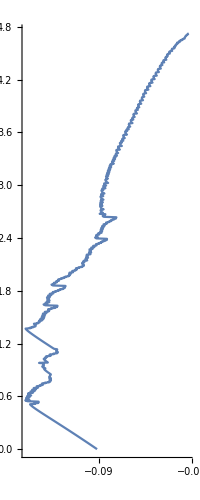

```mathematica
rear=ListLinePlot[Partition[Riffle[𝒳[[All,1]],𝒵],2],AspectRatio->True]
```

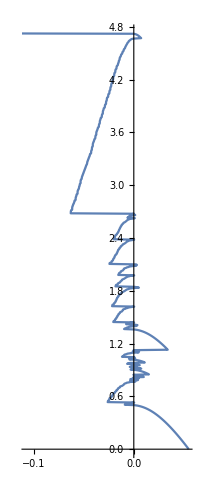

```mathematica
front=ListLinePlot[Partition[Riffle[𝒳[[All,2]],𝒵],2] ,AspectRatio->True]
```

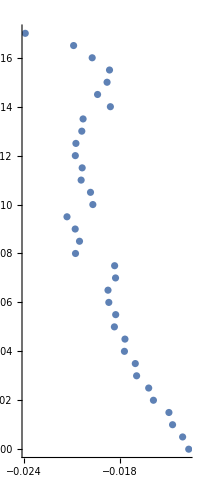

```mathematica
ListPlot[Partition[Riffle[𝒪,𝒵],2] ,AspectRatio->True]
```

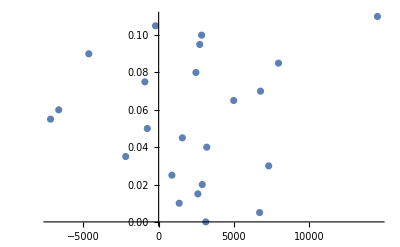

```mathematica
ListPlot[Partition[Riffle[𝒫,𝒵],2] ]
```

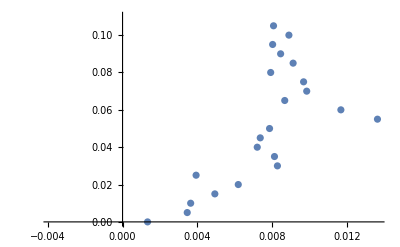

```mathematica
ListPlot[Partition[Riffle[ℛ𝒸,𝒵],2] ]
```

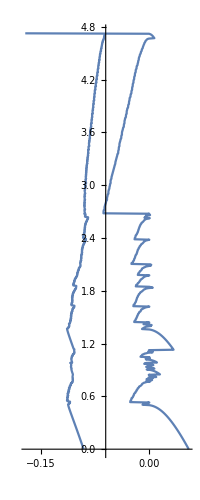

```mathematica
Show[{rear,front},AspectRatio->True,PlotRange->All]
```

```mathematica
ArcTan[Θ] // Mean
```

{0.0620616,0.0393942}

```mathematica
Last[𝒳]
```

Last::nolast: {} has zero length and no last element.

Last[{}]

This represents the solution of the moving line source with thickness of the plate thick, this is 3d solution in cylindrical coordinates:

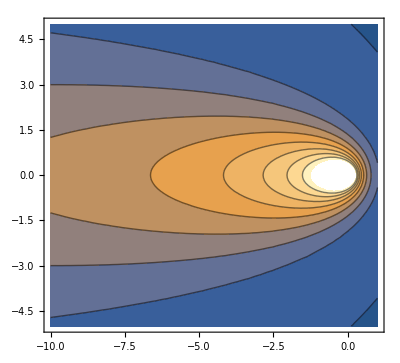

```mathematica
Tn[x_,y_,P_,thick_]:=Ta + P/(2π λ thick)Exp[-v x / (2 κ)] BesselK[0,v* Norm[{x,y}]/(2 κ)];
ContourPlot[Tn[x,y,245,1.], {x,-10,1},{y,-5,5}, AspectRatio->True]
```

```mathematica
r1 = FindRoot[Tn[x,0, 2450,1.] == Tv, {x,4}]
```

{x→-13.1836}

Solution of the moving point in 2d case :

```mathematica
Clear[T2D]
```

```mathematica
T2D[x_,y_,P_] :=Ta+ P/(2π λ)Exp[-v x / (2 κ)] BesselK[0,v* Norm[{x,y}]/(2 κ)];
```

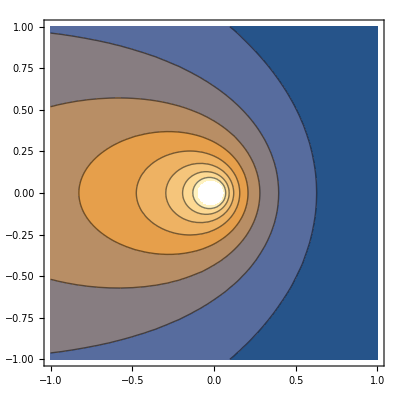

```mathematica
ContourPlot[T2D[x,y,245],{x,-1.,1},{y,-1,1}, AspectRatio->True]
```

```mathematica
r1 = NSolve[T2D[x,0, PL] == Tv, x, Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-28.4159},{x→0.668721}}

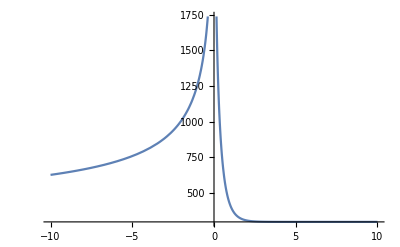

```mathematica
Plot[T2D[x,0,245],{x,-10,10}]
```

```mathematica
T2D[-1,0,2450]
```

10519.4

Different Rosenthal solution:

```mathematica
v=40;
```

```mathematica
Trosen[x_,y_,P_,dis_]:=Ta+P/(2 π λ Norm[{x,y}])Exp[-v *(Norm[{x,y}]+dis)/(2κ)]
```

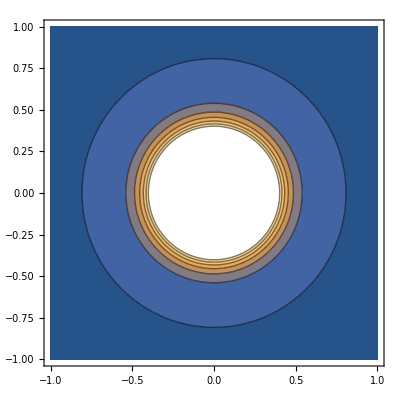

```mathematica
ContourPlot[Trosen[x,y,2450,0],{x,-1,1},{y,-1,1}, AspectRatio->True]
```

```mathematica
Tn[-1,0.000001]
```

1215.08-16090.8 ⅈ

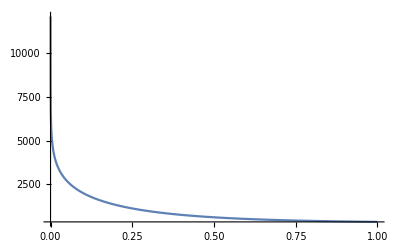

```mathematica
Plot[Tn[x,0],{x,-1,1}, PlotRange->All]
```

```mathematica
T[r,π]/.r->r1
```

{298+907.258 ⅇ^(1.32979 (x→0.0311167+8.72693×10^-17 ⅈ)) BesselK[0,1.32979 (x→0.0311167+8.72693×10^-17 ⅈ)]}

```mathematica
(2 PL)/(π rf0^2)
```

(75 π)/(F^2 M^4 wave^2)

```mathematica
(π PL)/(2 F^2 M^4)
```

(75 π)/(F^2 M^4)

```mathematica
qvr[0.8]
```

((-298+Tv) v λ (-1+BesselK[1,0.04 v]))/(20 BesselK[0,0.04 v])

```mathematica
f[x_]:=Abs[x]
```

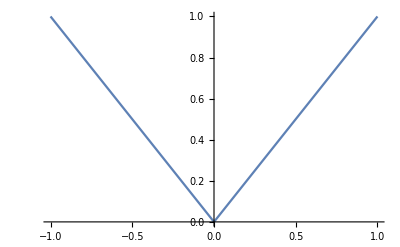

```mathematica
Plot[f[x],{x,-1,1}]
```

# Absorption

The plasma absorption can be described by Beer-Lambert law:
I_a(z)/I_i(0) = 1-I_t(z)/I_i(0)=1-exp(-α_iB z)
where I_i -is the incident intensity, I_t-the transmitted intensity and I_a is the intensity absorbed when passing path z. For the plasma absorption coefficient due to
inverse Bremsstrahlung α_iB that is temperature dependent. Mean value of 100 m^-1 is used.
Absorbed fraction of the metal vapour plume over the workpiece is known by estimating height
h_pl of the plume : 
α_pl=1-exp(-α_iB h_pl)
The remaining radiation  is transmitted and passes the plume. The power hitting the workpiece outside
the keyhole is strongly reflected and only small part is absorbed. The first plasma absorption before
hitting the keyhole wall:
α_(iB,1)= 1-exp(-α_iBd/2)
The first Fresnel absorption at each point is included in the energy balance by multiplying the local beam intensity by the Fresnel absorption coefficient.
After n_mr reflections, assuming geometrical optics, the part of the remaining intensity I_rn:
I_rn/I_i=(ρ_Fr)^nmr
where ρ_Fr is  the Fresnel reflection coefficient, which is in general angle-dependent.
The approximation of the keyhole profile with mean wall angle θ_w the angle of reflection θ_r=2 n_mr θ_w

The number of the reflections is defined by counting them up to the limiting angle of the reflected beam:
θ_r≥π/2..
n_mr=(π/2)/(2 θ_w)=π/(4 θ_w)
If the first reflection, which is separately considered in the energy balance.
Using previous equation for the number of reflections:
ρ_mr=[ρ_Fr(θ=π/2)]^(nmr-1)
Consequently the absorption coefficient α_mr:
α_mr=1-ρ_mr

During the reflections the rays cross plasma and are partially absorbed by it. 
α_(iB,mr)=1-exp(-α_iB3d/2)

The of the incident intensities damped by the plume minus the remaining intensity I_r leaving the
keyhole:
I_(a,Fr)+I_(a,mr)+I_(a,iB)=(1-α_pl)I(x,z)-I_r=f(θ_w) 
where:
I_r=(1-α_pl)(1-α_(iB,1))(1-α_Fr) x(1-α_mr)(1-α_(iB,mr))I(x,z)

I_(a,Fr)=(1-α_pl)*(1-α_(iB,1))α_Fr I(x,z)
I_(a,mr)=(1-α_pl)*(1-α_(iB,1))(1-α_Fr)α_mrI(x,z)
I_(a,iB)=(1-α_pl)(α_(iB,1)+α_(iB,mr)(1-α_(iB,1))x(1-α_Fr)(1-α_mr)) I(x,z)

```mathematica
Subscript[α, pl] = 1-Exp[-Subscript[α, iB] * Subscript[h, pl]];
nmr = π/(4 θw);
```

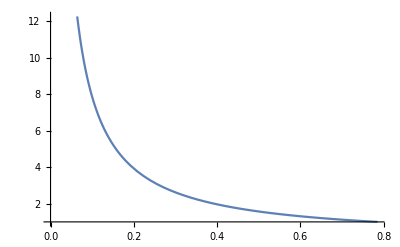

```mathematica
Plot[π/(4 θ), {θ,0,π/4}]
```

General::munfl: 0.8^48950. is too small to represent as a normalized machine number; precision may be lost.

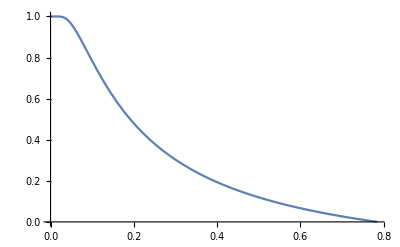

```mathematica
With[{ρ=0.8},Plot[1-ρ^(π/(4θ)-1), {θ,0,π/4}]]
```

Reflections from the keyhole, the first reflection is calculated separately in the energy balance. The rest reflections
can be approximated from the multiple reflections:

```mathematica
ρmr = ρFr^(nmr-1);
αmr = 1-ρmr;
```

This effect of the partial absorption of the intensity  can be modeled:

```mathematica
Subscript[α, iBmr]=1-Exp[-Subscript[α, iB] 3d/2];
```

After the first iteration of the algorithm we calculate the absorptions using the next sequence:

```mathematica
IaFr[x_,z_]:= (1-Subscript[α, pl])(1-Subscript[α, iB1])*Subscript[α, mr] *Ia[x,z];
Iamr[x_,z_]:= (1-Subscript[α, pl])(1-Subscript[α, iB1])*(1-Subscript[α, Fr])Subscript[α, mr] *Ia[x,z];
IaiB[x_,z_]:= (1-Subscript[α, pl])(Subscript[α, iB1]+Subscript[α, iBmr] *(1-Subscript[α, iB1])(1-Subscript[α, Fr])(1-Subscript[α, mr]) )*Ia[x,z];
Ir[x_,z_]:= (1-Subscript[α, pl])(1-Subscript[α, iB1])*(1-Subscript[α, Fr])(1-Subscript[α, mr])(1-Subscript[α, iBmr])*Ia[x,z];
```

Parameters used in the calculation:
Laser power (cw)  Pl  4kW
Wavelength             λ   10.6   μm
Polarisation            -    unpolarized -
Beam quality          M^2   5.0
Beam mode          TEM  TEM_00
Focal length          f         200    mm
Beam diameter on optics  D_b     34
Focusing number     F = f / D_b       6.0
Focal radius               r_f0       203 , μm
Rayleigh length        z_r      2.5    mm
Absorption coefficient Bremsstrahlung    α_iB  100 m^-1
Focal plane                 z_0    optimized 0.7
welding speed           v        50  mm/s
Initial depth of keyhole  d    3.5 mm
Material                      mild steel
	λ                          45 W/mK
	κ                          18.8 mm^2/s
Weld                             blind weld

```mathematica
PL = 4 10^3;
M = Sqrt[5];
F = 6.0;
wave =10.6 10^-3;
rf0 = 0.203;
zr = 2.5;
z0 = 0.7;
v = 50.0;
Subscript[α, iB]= 100 10^-3;
Subscript[h, pl] = 0.2;
d =5.5; 
(* this is the function of the incident angle *)
αFr[θ_]:= Module[{n=14.8, k=15.5}, Ap[θ]:= 4 n Cos[θ]/((n^2+k^2)Cos[θ]^2+2 n Cos[θ] + 1);  
As[θ]:= 4 n Cos[θ]/((n^2+k^2)+Cos[θ]^2+2 n Cos[θ]); (As[θ]+Ap[θ])*0.5];
Subscript[ρ, Fr]=1-αFr[θ];
Ta = 298;
Tv = 2900+273;
κ = 18.8; λ= 45*10^-3;
```

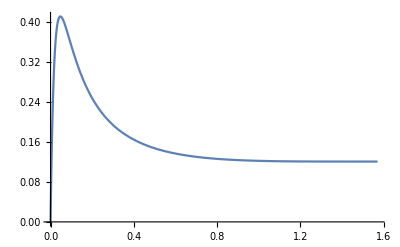

```mathematica
Plot[αFr[π/2-θ], {θ,0,π/2}, PlotRange->All]
```

# Gaseous phase

The state of the vapour inside the keyhole is calculated for each element after having calculate the keyhole profile.

The degree of ionization as a function of temperature is Saha’s equation:
n_en_i/n_n = 2(g_o)_i/g_n (2πmkT)/h^3exp(-W_i/kT)
where n_e,n_i and n_n are the particle densities of electrons, ions and ground state atoms respectively and g_0 is the statistical weight. The electron mass m_e, Planck’s constant ℏ = h/2π and Boltzmann constant k.
W_i denotes the work for ionization.

The dominant absorption mechanism in a plasma for CO2 laser radiation is the mechanism of inverse Bremsstrahlung.  Linear plasma absorption coefficient α_iB:

α_iB= (Z^2 e^6 n_e)/(6 √3 ℏω^3 m_e^2 c_0 ϵ_0^3(1-(ω_pe/ω)^2)) x(m/(2πkT))(1-exp(-ℏω/kT))ḡ

```mathematica
l1 = {1,2,3,4}; l2 = {5,6,7,8};
Mean[{l1,l2}]
```

{3,4,5,6}